# ColorPlanarGraphFaces

Color the faces of a planar graph

## Definition

```mathematica
ColorPlanarGraphFaces//ClearAll
ColorPlanarGraphFaces[graph_?PlanarGraphQ]:=Block[{coords,colors},coords=AssociationThread[VertexList[graph]->GraphEmbedding[graph]];colors=FindPlanarColoring[graph,ColorData[106,"ColorList"]];Graphics[Table[Style[Polygon[PlanarFaceList[graph][[i]]/.coords],colors[[i]]],{i,Length[colors]}]]]
ColorPlanarGraphFaces[graph_?PlanarGraphQ,colors_List]:=Block[{coords},coords=AssociationThread[VertexList[graph]->GraphEmbedding[graph]];Graphics[Table[Style[Polygon[PlanarFaceList[graph][[i]]/.coords],colors[[i]]],{i,Length[colors]}]]]
```

## Documentation

### Usage

ColorPlanarGraphFaces[graph]

colors the faces of the planar graph graph.

ColorPlanarGraphFaces[graph,colors]

colors the faces of the planar graph graph with colors.

### Details & Options

The function's timing depends on FindPlanarColoring.

For colors use ColorData[integer,"ColorList"].

The output is a Graphics object. I would like to return a Graph object but I'm not sure how to. I based on this on a documentation example for FindPlanarColoring. This means that the function cannot be computed on afterwards because GraphQ fails.

## Examples

### Basic Examples

Color a maximally planar graph:

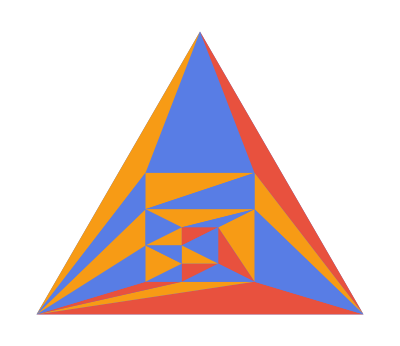

```mathematica
ColorPlanarGraphFaces[GraphData[{"ChromaticallyEquivalent",{16,6,1}}]]
```

Color the Heawood four color:

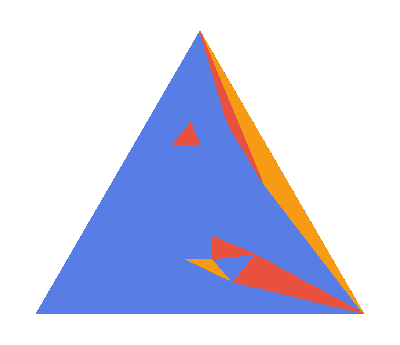

```mathematica
ColorPlanarGraphFaces[GraphData["HeawoodFourColorGraph"]]
```

Color an Apollonian graph:

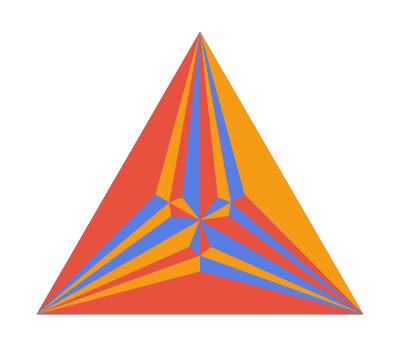

```mathematica
ColorPlanarGraphFaces[GraphData[{"Apollonian",3}]]
```

### Scope

Text about additional examples expanding scope (and see other sections for options, applications, etc):

```mathematica
MyFunction[x,y,z]
```

x y z

### Options

Ask the function for a particular set of colors:

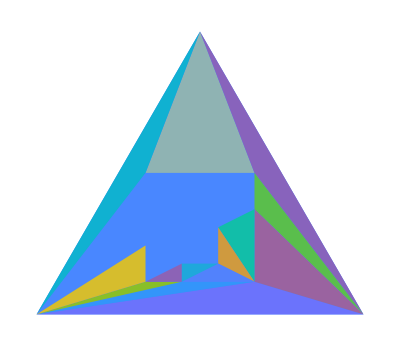

```mathematica
ColorPlanarGraphFaces[GraphData[{"ChromaticallyEquivalent",{16,6,1}}],ColorData[107,"ColorList"]]
```

### Applications

### Properties and Relations

### Possible Issues

The output is a Graphics object, not a graph:

```mathematica
GraphQ[ColorPlanarGraphFaces[GraphData[{"ChromaticallyEquivalent",{16,6,1}}],ColorData[107,"ColorList"]]]
```

False

### Neat Examples

## Source & Additional Information

### Contributed By

Peter Cullen Burbery

### Keywords

planar coloring

maximally planar graphs

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Repository Tools
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction
 Wolfram Physics Project |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Just For Fun
 Machine Learning
 Programming Utilities
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics

### Related Symbols

FindPlanarColoring

PlanarGraphQ

### Related Resource Objects

ColorGraphEdges

ColorGraphVertices

### Source/Reference Citation

Source, reference or citation information

### Links

Link to other related material

### Tests

```mathematica
MyFunction[x,y]
```

x y

### Compatibility

#### Wolfram Language Version

13.1+

#### Operating System

Windows |  Mac |  Unix

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

## Author Notes

Additional information about limitations, issues, etc.

## Submission Notes

This function is based on a documentation example for FindPlanarColoring.